### Start choosing the example:

```mathematica
t=22;
beta =0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x]
```

Log[x]

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5,6,7},Adjacency Matrix→{{0,1,1,0,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,1,0,0},{0,0,0,0,0,1,0},{0,0,0,0,0,1,1},{0,0,0,0,0,0,1},{0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,I1},{2,I2}},Exit Vertices and Terminal Costs→{{5,U1},{6,U2},{7,U3}},Switching Costs→{}|>

```mathematica
AdjacencyGraph[Data["Vertices List"],Data["Adjacency Matrix"],VertexLabels->"Name"]
```

-Graphics-

### Look at the output bellow before trying to rerun!

```mathematica
(*With U2->2, agents don't exit through 6. running with U2->U2 to determine the largest value for which we get some current, hence unicity.*)
```

```mathematica
d2e= D2E[Data/.{I1-> 2,I2->2, U1-> 1,U2->1,U3->0}];
```

```mathematica
CriticalCongestionSolver[d2e]
```

It took 0.093242 to Clean the equalities and get 
NonNegative[28/15+j10/15+j11/15+j17-j24/15-jt12]&&NonNegative[jt13+jt14]&&NonNegative[28/15+j10/15+j11/15+j17-j24/15]&&NonNegative[22/15+(4 j10)/15+(4 j11)/15+j17+j20-(4 j24)/15-jt20-jt23]&&NonNegative[38/15-(4 j10)/15-(4 j11)/15+(4 j24)/15+jt28+jt31]&&NonNegative[22/15+(4 j10)/15+(4 j11)/15+j20-(4 j24)/15]&&NonNegative[-22/15+(11 j10)/15+(11 j11)/15+j21-(11 j24)/15]&&NonNegative[-22/15+(26 j10)/15+(11 j11)/15-(26 j24)/15+jt51]&&NonNegative[82/15-(41 j10)/15-(26 j11)/15+(41 j24)/15]&&NonNegative[j10]&&NonNegative[j11]&&NonNegative[-22/15+(41 j10)/15+(11 j11)/15-(41 j24)/15]&&NonNegative[2+j17-jt12]&&NonNegative[-32/15+j10/15+j11/15-j24/15+jt13+jt14]&&NonNegative[j17]&&NonNegative[28/15+j10/15+j11/15+j17+j20-j24/15-jt20-jt23]&&NonNegative[jt28+jt31]&&NonNegative[j20]&&NonNegative[j21]&&NonNegative[jt51]&&NonNegative[j24]&&NonNegative[2+j17-jt12]&&NonNegative[-32/15+j10/15+j11/15-j24/15+jt13+jt14]&&NonNegative[4+j17-jt12-jt13-jt14]&&NonNegative[-2-j17+jt12+jt13+jt14]&&NonNegative[28/15+j10/15+j11/15+j17-j24/15-jt12]&&NonNegative[j17]&&NonNegative[2-jt12]&&NonNegative[jt12]&&NonNegative[jt13]&&NonNegative[jt14]&&NonNegative[-2/3+j10/3+j11/3+j17+j20-j24/3+jt14-jt20-jt23-jt28-jt31]&&NonNegative[38/15-(4 j10)/15-(4 j11)/15+(4 j24)/15-jt14+jt28+jt31]&&NonNegative[-22/15-(4 j10)/15-(4 j11)/15-j17-j20+(4 j24)/15+jt13+jt20+jt23+jt28+jt31]&&NonNegative[22/15+(4 j10)/15+(4 j11)/15+j17+j20-(4 j24)/15-jt13-jt20-jt23]&&NonNegative[28/15+j10/15+j11/15+j17-j24/15-jt20]&&NonNegative[jt20]&&NonNegative[j17-jt23]&&NonNegative[22/15+(4 j10)/15+(4 j11)/15+j20-(4 j24)/15-jt20]&&NonNegative[jt23]&&NonNegative[j20-jt23]&&NonNegative[jt25]&&NonNegative[jt26]&&NonNegative[38/15-(4 j10)/15-(4 j11)/15+(4 j24)/15-jt25-jt26+jt28+jt31]&&NonNegative[jt28]&&NonNegative[-22/15+(26 j10)/15+(11 j11)/15-(26 j24)/15-jt26+jt51]&&NonNegative[22/15-(26 j10)/15-(11 j11)/15+j21+(26 j24)/15+jt26-jt28-jt51]&&NonNegative[jt31]&&NonNegative[-22/15+(11 j10)/15+(11 j11)/15+j21-(11 j24)/15-jt25]&&NonNegative[22/15-(11 j10)/15-(11 j11)/15-j21+(11 j24)/15+jt25-jt31+jt51]&&NonNegative[j21-jt44]&&NonNegative[jt38]&&NonNegative[22/15+(4 j10)/15+(4 j11)/15+j20-j21-(4 j24)/15-jt38+jt44]&&NonNegative[j20-jt43]&&NonNegative[j10-jt38]&&NonNegative[-22/15-(4 j10)/15+(11 j11)/15-j20+j21-(11 j24)/15+jt38+jt43]&&NonNegative[jt43]&&NonNegative[jt44]&&NonNegative[j24-jt43-jt44]&&NonNegative[j24]&&NonNegative[-22/15+(26 j10)/15+(11 j11)/15-(41 j24)/15+jt51]&&NonNegative[jt51]&&NonNegative[j10-jt51]&&16/5+(2 j10)/5+(2 j11)/5-(2 j24)/5+u10≥u13&&u14≤10/3+j10/3+j11/3-j24/3+u10&&-22/15+(11 j10)/15+(11 j11)/15-(11 j24)/15+u10≤1&&1≥u10&&0≥-j10+j24+u10&&(2+j17-jt12==0||28/15+j10/15+j11/15+j17-j24/15-jt12==0)&&(-32/15+j10/15+j11/15-j24/15+jt13+jt14==0||jt13+jt14==0)&&(j17==0||28/15+j10/15+j11/15+j17-j24/15==0)&&(28/15+j10/15+j11/15+j17+j20-j24/15-jt20-jt23==0||22/15+(4 j10)/15+(4 j11)/15+j17+j20-(4 j24)/15-jt20-jt23==0)&&(jt28+jt31==0||38/15-(4 j10)/15-(4 j11)/15+(4 j24)/15+jt28+jt31==0)&&(j20==0||22/15+(4 j10)/15+(4 j11)/15+j20-(4 j24)/15==0)&&(j21==0||-22/15+(11 j10)/15+(11 j11)/15+j21-(11 j24)/15==0)&&(jt51==0||-22/15+(26 j10)/15+(11 j11)/15-(26 j24)/15+jt51==0)&&(j24==0||j10==0)&&(2+j17-jt12==0||-32/15+j10/15+j11/15-j24/15+jt13+jt14==0)&&(jt13==0||-2/3+j10/3+j11/3+j17+j20-j24/3+jt14-jt20-jt23-jt28-jt31==0)&&(jt14==0||-22/15-(4 j10)/15-(4 j11)/15-j17-j20+(4 j24)/15+jt13+jt20+jt23+jt28+jt31==0)&&(38/15-(4 j10)/15-(4 j11)/15+(4 j24)/15-jt14+jt28+jt31==0||22/15+(4 j10)/15+(4 j11)/15+j17+j20-(4 j24)/15-jt13-jt20-jt23==0)&&(28/15+j10/15+j11/15+j17-j24/15-jt20==0||j17-jt23==0)&&(jt20==0||jt23==0)&&(22/15+(4 j10)/15+(4 j11)/15+j20-(4 j24)/15-jt20==0||j20-jt23==0)&&(jt25==0||jt28==0)&&(jt26==0||jt31==0)&&(-22/15+(26 j10)/15+(11 j11)/15-(26 j24)/15-jt26+jt51==0||-22/15+(11 j10)/15+(11 j11)/15+j21-(11 j24)/15-jt25==0)&&(j21-jt44==0||j20-jt43==0)&&(jt38==0||jt43==0)&&(j10-jt38==0||jt44==0)&&(j24==0||jt51==0)&&(28/15+j10/15+j11/15+j17-j24/15-jt12==0||j17==0)&&(4+j17-jt12-jt13-jt14==0||16/5+(2 j10)/5+(2 j11)/5-(2 j24)/5+u10-u13==0)&&(-2-j17+jt12+jt13+jt14==0||16/5+(2 j10)/5+(2 j11)/5-(2 j24)/5+u10-u13==0)&&(2-jt12==0||10/3+j10/3+j11/3-j24/3+u10-u14==0)&&(jt12==0||10/3+j10/3+j11/3-j24/3+u10-u14==0)&&(38/15-(4 j10)/15-(4 j11)/15+(4 j24)/15-jt25-jt26+jt28+jt31==0||37/15-(11 j10)/15-(11 j11)/15+(11 j24)/15-u10==0)&&(22/15-(26 j10)/15-(11 j11)/15+j21+(26 j24)/15+jt26-jt28-jt51==0||37/15-(11 j10)/15-(11 j11)/15+(11 j24)/15-u10==0)&&(22/15-(11 j10)/15-(11 j11)/15-j21+(11 j24)/15+jt25-jt31+jt51==0||37/15-(11 j10)/15-(11 j11)/15+(11 j24)/15-u10==0)&&(22/15+(4 j10)/15+(4 j11)/15+j20-j21-(4 j24)/15-jt38+jt44==0||1-u10==0)&&(-22/15-(4 j10)/15+(11 j11)/15-j20+j21-(11 j24)/15+jt38+jt43==0||1-u10==0)&&(j24-jt43-jt44==0||1-u10==0)&&(-22/15+(26 j10)/15+(11 j11)/15-(41 j24)/15+jt51==0||j10-j24-u10==0)&&(j10-jt51==0||j10-j24-u10==0)

It took 102.488 to NewReduce to jt44==0&&jt43==0&&jt38==1&&jt31==0&&jt28==0&&jt26==1&&jt25==0&&u14==5&&u13==5&&u10==1&&jt51==0&&jt23==0&&jt20==2&&jt14==2&&jt13==0&&jt12==2&&j24==0&&j21==0&&j20==0&&j17==0&&j11==1&&j10==1

DataToEquations: Critical congestion solved.

{True,<|j1→0,j12→2,j13→2,j14→2,j15→0,j16→0,j18→0,j19→0,j2→2,j22→0,j23→0,j25→0,j26→0,j27→0,j28→0,j3→2,j4→0,j5→2,j6→2,j7→0,j8→1,j9→1,jt1→0,jt10→0,jt11→0,jt15→0,jt16→0,jt17→0,jt18→0,jt19→0,jt2→0,jt21→0,jt22→0,jt24→0,jt27→1,jt29→0,jt3→0,jt30→0,jt32→0,jt33→0,jt34→0,jt35→0,jt36→0,jt37→0,jt39→1,jt4→0,jt40→0,jt41→0,jt42→0,jt45→0,jt46→0,jt47→0,jt48→0,jt49→0,jt5→0,jt50→1,jt52→1,jt53→0,jt54→0,jt6→2,jt7→0,jt8→0,jt9→0,u1→5,u11→1,u12→0,u15→5,u16→3,u17→3,u18→3,u19→1,u2→5,u20→1,u21→1,u22→0,u23→1,u24→0,u25→1,u26→0,u27→5,u28→5,u3→5,u4→3,u5→3,u6→3,u7→1,u8→1,u9→1,j10→1,j11→1,j17→0,j20→0,j21→0,j24→0,jt12→2,jt13→0,jt14→2,jt20→2,jt23→0,jt25→0,jt26→1,jt28→0,jt31→0,jt38→1,jt43→0,jt44→0,jt51→0,u10→1,u13→5,u14→5|>}

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 2,I2->2, U1-> 1,U2->1,U3->0}];//Timing//AbsoluteTiming
```

DataToEquations: Triangle inequalities for switching costs: {}
DataToEquations: Reduced: True

DataToEquations: The switching costs are compatible.

DataToEquations: Finished assembling strucural equations.

Reducing the structural system ...

DataToEquations: Critical case ...

```mathematica
MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]]
```

<|{2,1->2}→0,{3,1->3}→53/26,{4,2->4}→51/26,{4,3->4}→0,{5,3->5}→28/13,{6,4->6}→24/13,{6,5->6}→0,{7,5->7}→1,{ex239,5->ex239}→41/26,{7,6->7}→37/26,{ex240,6->ex240}→0,{ex241,7->ex241}→63/26,{1,en237->1}→2,{2,en238->2}→2,{1,1->2}→1/26,{1,1->3}→0,{2,2->4}→0,{3,3->4}→3/26,{3,3->5}→0,{4,4->6}→0,{5,5->6}→11/26,{5,5->7}→0,{5,5->ex239}→0,{6,6->7}→0,{6,6->ex240}→0,{7,7->ex241}→0,{en237,en237->1}→0,{en238,en238->2}→0|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 1,I2->2, U1-> 1,U2->2,U3->3}];//Timing//AbsoluteTiming
```

DataToEquations: Triangle inequalities for switching costs: {}
DataToEquations: Reduced: True

DataToEquations: The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 102.257 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{102.402,{111.931,Null}}

```mathematica
d2emult = D2E[Data/.{I1-> 2,I2->6, U1-> 1,U2->2,U3->0}];
```

```mathematica
{timemult,{systemmult,resultmult}}=CriticalCongestionSolver[d2emult]
```

It took 0.07924 to Clean the equalities and get 
NonNegative[64/15+j10/15+j11/15+j17-j24/15-jt12]&&NonNegative[jt13+jt14]&&NonNegative[64/15+j10/15+j11/15+j17-j24/15]&&NonNegative[46/15+(4 j10)/15+(4 j11)/15+j17+j20-(4 j24)/15-jt20-jt23]&&NonNegative[74/15-(4 j10)/15-(4 j11)/15+(4 j24)/15+jt28+jt31]&&NonNegative[46/15+(4 j10)/15+(4 j11)/15+j20-(4 j24)/15]&&NonNegative[-46/15+(11 j10)/15+(11 j11)/15+j21-(11 j24)/15]&&NonNegative[-46/15+(26 j10)/15+(11 j11)/15-(26 j24)/15+jt51]&&NonNegative[166/15-(41 j10)/15-(26 j11)/15+(41 j24)/15]&&NonNegative[j10]&&NonNegative[j11]&&NonNegative[-46/15+(41 j10)/15+(11 j11)/15-(41 j24)/15]&&NonNegative[6+j17-jt12]&&NonNegative[-56/15+j10/15+j11/15-j24/15+jt13+jt14]&&NonNegative[j17]&&NonNegative[64/15+j10/15+j11/15+j17+j20-j24/15-jt20-jt23]&&NonNegative[jt28+jt31]&&NonNegative[j20]&&NonNegative[j21]&&NonNegative[jt51]&&NonNegative[j24]&&NonNegative[6+j17-jt12]&&NonNegative[-56/15+j10/15+j11/15-j24/15+jt13+jt14]&&NonNegative[8+j17-jt12-jt13-jt14]&&NonNegative[-6-j17+jt12+jt13+jt14]&&NonNegative[64/15+j10/15+j11/15+j17-j24/15-jt12]&&NonNegative[j17]&&NonNegative[6-jt12]&&NonNegative[jt12]&&NonNegative[jt13]&&NonNegative[jt14]&&NonNegative[-2/3+j10/3+j11/3+j17+j20-j24/3+jt14-jt20-jt23-jt28-jt31]&&NonNegative[74/15-(4 j10)/15-(4 j11)/15+(4 j24)/15-jt14+jt28+jt31]&&NonNegative[-46/15-(4 j10)/15-(4 j11)/15-j17-j20+(4 j24)/15+jt13+jt20+jt23+jt28+jt31]&&NonNegative[46/15+(4 j10)/15+(4 j11)/15+j17+j20-(4 j24)/15-jt13-jt20-jt23]&&NonNegative[64/15+j10/15+j11/15+j17-j24/15-jt20]&&NonNegative[jt20]&&NonNegative[j17-jt23]&&NonNegative[46/15+(4 j10)/15+(4 j11)/15+j20-(4 j24)/15-jt20]&&NonNegative[jt23]&&NonNegative[j20-jt23]&&NonNegative[jt25]&&NonNegative[jt26]&&NonNegative[74/15-(4 j10)/15-(4 j11)/15+(4 j24)/15-jt25-jt26+jt28+jt31]&&NonNegative[jt28]&&NonNegative[-46/15+(26 j10)/15+(11 j11)/15-(26 j24)/15-jt26+jt51]&&NonNegative[46/15-(26 j10)/15-(11 j11)/15+j21+(26 j24)/15+jt26-jt28-jt51]&&NonNegative[jt31]&&NonNegative[-46/15+(11 j10)/15+(11 j11)/15+j21-(11 j24)/15-jt25]&&NonNegative[46/15-(11 j10)/15-(11 j11)/15-j21+(11 j24)/15+jt25-jt31+jt51]&&NonNegative[j21-jt44]&&NonNegative[jt38]&&NonNegative[46/15+(4 j10)/15+(4 j11)/15+j20-j21-(4 j24)/15-jt38+jt44]&&NonNegative[j20-jt43]&&NonNegative[j10-jt38]&&NonNegative[-46/15-(4 j10)/15+(11 j11)/15-j20+j21-(11 j24)/15+jt38+jt43]&&NonNegative[jt43]&&NonNegative[jt44]&&NonNegative[j24-jt43-jt44]&&NonNegative[j24]&&NonNegative[-46/15+(26 j10)/15+(11 j11)/15-(41 j24)/15+jt51]&&NonNegative[jt51]&&NonNegative[j10-jt51]&&28/5+(2 j10)/5+(2 j11)/5-(2 j24)/5+u10≥u13&&u14≤22/3+j10/3+j11/3-j24/3+u10&&-46/15+(11 j10)/15+(11 j11)/15-(11 j24)/15+u10≤1&&2≥u10&&0≥-j10+j24+u10&&(6+j17-jt12==0||64/15+j10/15+j11/15+j17-j24/15-jt12==0)&&(-56/15+j10/15+j11/15-j24/15+jt13+jt14==0||jt13+jt14==0)&&(j17==0||64/15+j10/15+j11/15+j17-j24/15==0)&&(64/15+j10/15+j11/15+j17+j20-j24/15-jt20-jt23==0||46/15+(4 j10)/15+(4 j11)/15+j17+j20-(4 j24)/15-jt20-jt23==0)&&(jt28+jt31==0||74/15-(4 j10)/15-(4 j11)/15+(4 j24)/15+jt28+jt31==0)&&(j20==0||46/15+(4 j10)/15+(4 j11)/15+j20-(4 j24)/15==0)&&(j21==0||-46/15+(11 j10)/15+(11 j11)/15+j21-(11 j24)/15==0)&&(jt51==0||-46/15+(26 j10)/15+(11 j11)/15-(26 j24)/15+jt51==0)&&(j24==0||j10==0)&&(6+j17-jt12==0||-56/15+j10/15+j11/15-j24/15+jt13+jt14==0)&&(jt13==0||-2/3+j10/3+j11/3+j17+j20-j24/3+jt14-jt20-jt23-jt28-jt31==0)&&(jt14==0||-46/15-(4 j10)/15-(4 j11)/15-j17-j20+(4 j24)/15+jt13+jt20+jt23+jt28+jt31==0)&&(74/15-(4 j10)/15-(4 j11)/15+(4 j24)/15-jt14+jt28+jt31==0||46/15+(4 j10)/15+(4 j11)/15+j17+j20-(4 j24)/15-jt13-jt20-jt23==0)&&(64/15+j10/15+j11/15+j17-j24/15-jt20==0||j17-jt23==0)&&(jt20==0||jt23==0)&&(46/15+(4 j10)/15+(4 j11)/15+j20-(4 j24)/15-jt20==0||j20-jt23==0)&&(jt25==0||jt28==0)&&(jt26==0||jt31==0)&&(-46/15+(26 j10)/15+(11 j11)/15-(26 j24)/15-jt26+jt51==0||-46/15+(11 j10)/15+(11 j11)/15+j21-(11 j24)/15-jt25==0)&&(j21-jt44==0||j20-jt43==0)&&(jt38==0||jt43==0)&&(j10-jt38==0||jt44==0)&&(j24==0||jt51==0)&&(64/15+j10/15+j11/15+j17-j24/15-jt12==0||j17==0)&&(8+j17-jt12-jt13-jt14==0||28/5+(2 j10)/5+(2 j11)/5-(2 j24)/5+u10-u13==0)&&(-6-j17+jt12+jt13+jt14==0||28/5+(2 j10)/5+(2 j11)/5-(2 j24)/5+u10-u13==0)&&(6-jt12==0||22/3+j10/3+j11/3-j24/3+u10-u14==0)&&(jt12==0||22/3+j10/3+j11/3-j24/3+u10-u14==0)&&(74/15-(4 j10)/15-(4 j11)/15+(4 j24)/15-jt25-jt26+jt28+jt31==0||61/15-(11 j10)/15-(11 j11)/15+(11 j24)/15-u10==0)&&(46/15-(26 j10)/15-(11 j11)/15+j21+(26 j24)/15+jt26-jt28-jt51==0||61/15-(11 j10)/15-(11 j11)/15+(11 j24)/15-u10==0)&&(46/15-(11 j10)/15-(11 j11)/15-j21+(11 j24)/15+jt25-jt31+jt51==0||61/15-(11 j10)/15-(11 j11)/15+(11 j24)/15-u10==0)&&(46/15+(4 j10)/15+(4 j11)/15+j20-j21-(4 j24)/15-jt38+jt44==0||2-u10==0)&&(-46/15-(4 j10)/15+(11 j11)/15-j20+j21-(11 j24)/15+jt38+jt43==0||2-u10==0)&&(j24-jt43-jt44==0||2-u10==0)&&(-46/15+(26 j10)/15+(11 j11)/15-(41 j24)/15+jt51==0||j10-j24-u10==0)&&(j10-jt51==0||j10-j24-u10==0)

NewReduce: ZAnd took 178.189 to get to 
(j10==2&&11 j11==9&&j17==0&&j20==0&&j21==1&&j24==0&&11 jt12==49&&jt13==0&&11 jt14==39&&11 jt20==42&&jt23==0&&jt25==0&&jt26==0&&jt28+jt31==0&&jt38==2&&jt43==0&&jt51==0&&u10==2&&11 u13==96&&11 u14==113&&NonNegative[-jt28]&&NonNegative[jt28]&&NonNegative[1-jt44]&&NonNegative[-jt44]&&NonNegative[jt44]&&NonNegative[9/11+jt44])||(j10==2&&11 j11==9&&j17==0&&j20==0&&j21==1&&j24==0&&11 jt12==49&&jt13==0&&11 jt14==39&&11 jt20==42&&jt23==0&&jt25==0&&jt26==0&&jt28+jt31==0&&jt43==0&&jt44==0&&jt51==0&&u10==2&&11 u13==96&&11 u14==113&&NonNegative[-jt28]&&NonNegative[jt28]&&NonNegative[2-jt38]&&NonNegative[31/11-jt38]&&NonNegative[-2+jt38]&&NonNegative[jt38])||(j10==2&&11 j11==9&&j17==0&&j20==0&&j21==1&&j24==0&&11 jt12==49&&jt13==0&&11 jt14==39&&11 jt20==42&&jt23==0&&jt25==0&&jt28==0&&jt31==0&&jt38==2&&jt43==0&&jt51==0&&u10==2&&11 u13==96&&11 u14==113&&NonNegative[690/11-15 jt26]&&NonNegative[1-jt26]&&NonNegative[jt26]&&NonNegative[1-jt44]&&NonNegative[-jt44]&&NonNegative[jt44]&&NonNegative[9/11+jt44])||(j10==2&&11 j11==9&&j17==0&&j20==0&&j21==1&&j24==0&&11 jt12==49&&jt13==0&&11 jt14==39&&11 jt20==42&&jt23==0&&jt25==0&&jt28==0&&jt31==0&&jt43==0&&jt44==0&&jt51==0&&u10==2&&11 u13==96&&11 u14==113&&NonNegative[690/11-15 jt26]&&NonNegative[1-jt26]&&NonNegative[jt26]&&NonNegative[2-jt38]&&NonNegative[31/11-jt38]&&NonNegative[-2+jt38]&&NonNegative[jt38])||(j10==2&&11 j11==9&&j17==0&&j20==0&&j21==1&&j24==0&&11 jt12==49&&jt13==0&&11 jt14==39&&11 jt20==42&&jt23==0&&jt26==1&&jt28==0&&jt31==0&&jt38==2&&jt43==0&&jt51==0&&u10==2&&11 u13==96&&11 u14==113&&NonNegative[35/11-jt25]&&NonNegative[-jt25]&&NonNegative[jt25]&&NonNegative[1-jt44]&&NonNegative[-jt44]&&NonNegative[jt44]&&NonNegative[9/11+jt44])||(j10==2&&11 j11==9&&j17==0&&j20==0&&j21==1&&j24==0&&11 jt12==49&&jt13==0&&11 jt14==39&&11 jt20==42&&jt23==0&&jt26==1&&jt28==0&&jt31==0&&jt43==0&&jt44==0&&jt51==0&&u10==2&&11 u13==96&&11 u14==113&&NonNegative[35/11-jt25]&&NonNegative[-jt25]&&NonNegative[jt25]&&NonNegative[2-jt38]&&NonNegative[31/11-jt38]&&NonNegative[-2+jt38]&&NonNegative[jt38])

NewReduce: Reduce took 0.014889 to get to 
0≤jt26≤1&&jt44==0&&jt38==2&&jt31==0&&jt28==0&&jt25==0&&u14==113/11&&u13==96/11&&u10==2&&jt51==0&&jt43==0&&jt23==0&&jt20==42/11&&jt14==39/11&&jt13==0&&jt12==49/11&&j24==0&&j21==1&&j20==0&&j17==0&&j11==9/11&&j10==2

It took 178.212 to NewReduce to 0≤jt26≤1&&jt44==0&&jt38==2&&jt31==0&&jt28==0&&jt25==0&&11 u14==113&&11 u13==96&&u10==2&&jt51==0&&jt43==0&&jt23==0&&11 jt20==42&&11 jt14==39&&jt13==0&&11 jt12==49&&j24==0&&j21==1&&j20==0&&j17==0&&11 j11==9&&j10==2

DataToEquations: The system does not have the original structure: 0≤jt26≤1&&jt44==0&&jt38==2&&jt31==0&&jt28==0&&jt25==0&&11 u14==113&&11 u13==96&&u10==2&&jt51==0&&jt43==0&&jt23==0&&11 jt20==42&&11 jt14==39&&jt13==0&&11 jt12==49&&j24==0&&j21==1&&j20==0&&j17==0&&11 j11==9&&j10==2

DataToEquations: Multiple solutions 
		0≤jt26≤1

DataToEquations: There are multiple solutions for the given data.

{0≤jt26≤1,<|j1→0,j12→3,j13→2,j14→6,j15→17/11,j16→0,j18→7/11,j19→0,j2→39/11,j22→0,j23→0,j25→0,j26→0,j27→0,j28→0,j3→49/11,j4→0,j5→46/11,j6→42/11,j7→0,j8→1,j9→46/11,jt1→17/11,jt10→0,jt11→17/11,jt15→0,jt16→7/11,jt17→0,jt18→0,jt19→7/11,jt2→0,jt21→0,jt22→0,jt24→0,jt27→46/11-jt26,jt29→1-jt26,jt3→0,jt30→jt26,jt32→0,jt33→0,jt34→0,jt35→0,jt36→0,jt37→1,jt39→9/11,jt4→0,jt40→0,jt41→0,jt42→0,jt45→0,jt46→0,jt47→0,jt48→0,jt49→0,jt5→0,jt50→1,jt52→2,jt53→0,jt54→0,jt6→2,jt7→0,jt8→0,jt9→0,u1→96/11,u11→2,u12→0,u15→113/11,u16→57/11,u17→64/11,u18→64/11,u19→1,u2→96/11,u20→2,u21→2,u22→0,u23→1,u24→0,u25→2,u26→0,u27→96/11,u28→113/11,u3→113/11,u4→57/11,u5→57/11,u6→64/11,u7→1,u8→1,u9→1,j10→2,j11→9/11,j17→0,j20→0,j21→1,j24→0,jt12→49/11,jt13→0,jt14→39/11,jt20→42/11,jt23→0,jt25→0,jt28→0,jt31→0,jt38→2,jt43→0,jt44→0,jt51→0,u10→2,u13→96/11,u14→113/11|>}

```mathematica
d2emult["jts"]
```

{jt1,jt2,jt3,jt4,jt5,jt6,jt7,jt8,jt9,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt30,jt31,jt32,jt33,jt34,jt35,jt36,jt37,jt38,jt39,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt50,jt51,jt52,jt53,jt54}

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 2,I2->6, U1-> 1,U2->2,U3->0}];//Timing//AbsoluteTiming
```

DataToEquations: Triangle inequalities for switching costs: {}
DataToEquations: Reduced: True

DataToEquations: The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 104.37 seconds to reduce with NewReduce!

DataToEquations: Mixed system:

DataToEquations: Possible multiple solutions 
{0≤jt355≤1,<|j302→0,j303→39/11,j305→0,j306→46/11,j310→46/11,j312→9/11,j313→3,j314→2,j315→6,j316→17/11,j317→0,j318→0,j319→7/11,j320→0,j321→0,j322→1,j323→0,j324→0,j326→0,j327→0,j328→0,j329→0,jt330→17/11,jt331→0,jt332→0,jt333→0,jt334→0,jt335→2,jt337→0,jt338→0,jt339→0,jt340→17/11,jt341→49/11,jt344→0,jt345→7/11,jt346→0,jt347→0,jt348→7/11,jt350→0,jt351→0,jt353→0,jt356→46/11-jt355,jt358→1-jt355,jt359→jt355,jt361→0,jt362→0,jt363→0,jt364→0,jt365→0,jt366→1,jt368→9/11,jt369→0,jt370→0,jt371→0,jt374→0,jt375→0,jt376→0,jt377→0,jt378→0,jt379→1,jt381→2,jt382→0,jt383→0,u384→96/11,u385→96/11,u386→113/11,u387→57/11,u388→57/11,u389→64/11,u390→1,u391→1,u392→1,u394→2,u395→0,u398→113/11,u399→57/11,u400→64/11,u401→64/11,u402→1,u403→2,u404→2,u405→0,u406→1,u407→0,u408→2,u409→0,u410→96/11,u411→113/11,j304→49/11,j307→42/11,j308→0,j309→1,j311→2,j325→0,jt336→0,jt342→0,jt343→39/11,jt349→42/11,jt352→0,jt354→0,jt357→0,jt360→0,jt367→2,jt372→0,jt373→0,jt380→0,u393→2,u396→96/11,u397→113/11|>}

DataToEquations: There are multiple solutions for the given data.

DataToEquations: Done.

{104.57,{112.413,Null}}

<|{1,1->2,1->3}→17/11,{1,1->2,en297->1}→0,{1,1->3,1->2}→0,{1,1->3,en297->1}→0,{1,en297->1,1->2}→0,{1,en297->1,1->3}→2,{2,1->2,2->4}→0,{2,1->2,en298->2}→0,{2,2->4,1->2}→0,{2,2->4,en298->2}→0,{2,en298->2,1->2}→17/11,{2,en298->2,2->4}→49/11,{3,1->3,3->4}→0,{3,1->3,3->5}→39/11,{3,3->4,1->3}→0,{3,3->4,3->5}→7/11,{3,3->5,1->3}→0,{3,3->5,3->4}→0,{4,2->4,3->4}→7/11,{4,2->4,4->6}→42/11,{4,3->4,2->4}→0,{4,3->4,4->6}→0,{4,4->6,2->4}→0,{4,4->6,3->4}→0,{5,3->5,5->6}→0,{5,3->5,5->7}→jt355,{5,3->5,5->ex299}→46/11-jt355,{5,5->6,3->5}→0,{5,5->6,5->7}→1-jt355,{5,5->6,5->ex299}→jt355,{5,5->7,3->5}→0,{5,5->7,5->6}→0,{5,5->7,5->ex299}→0,{5,5->ex299,3->5}→0,{5,5->ex299,5->6}→0,{5,5->ex299,5->7}→0,{6,4->6,5->6}→1,{6,4->6,6->7}→2,{6,4->6,6->ex300}→9/11,{6,5->6,4->6}→0,{6,5->6,6->7}→0,{6,5->6,6->ex300}→0,{6,6->7,4->6}→0,{6,6->7,5->6}→0,{6,6->7,6->ex300}→0,{6,6->ex300,4->6}→0,{6,6->ex300,5->6}→0,{6,6->ex300,6->7}→0,{7,5->7,6->7}→0,{7,5->7,7->ex301}→1,{7,6->7,5->7}→0,{7,6->7,7->ex301}→2,{7,7->ex301,5->7}→0,{7,7->ex301,6->7}→0|>

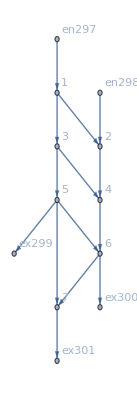

```mathematica
MFGEquations["jtvars"]/.MFGEquations["criticalreduced1"][[2]]
MFGEquations["FG"]
```

```mathematica
MFGEquations["EqAll"]/.(MFGEquations["criticalreduced1"][[2]])
```

True

```mathematica
MFGEquations["EqAllAll"]
```

NonNegative[j998]&&NonNegative[j999]&&NonNegative[j1000]&&NonNegative[j1001]&&NonNegative[j1002]&&NonNegative[j1003]&&NonNegative[j1004]&&NonNegative[j1005]&&NonNegative[j1006]&&NonNegative[j1007]&&NonNegative[j1008]&&NonNegative[j1009]&&NonNegative[j1010]&&NonNegative[j1011]&&NonNegative[j1012]&&NonNegative[j1013]&&NonNegative[j1014]&&NonNegative[j1015]&&NonNegative[j1016]&&NonNegative[j1017]&&NonNegative[j1018]&&NonNegative[j1019]&&NonNegative[j1020]&&NonNegative[j1021]&&NonNegative[j1022]&&NonNegative[j1023]&&NonNegative[j1024]&&NonNegative[j1025]&&NonNegative[jt1026]&&NonNegative[jt1027]&&NonNegative[jt1028]&&NonNegative[jt1029]&&NonNegative[jt1030]&&NonNegative[jt1031]&&NonNegative[jt1032]&&NonNegative[jt1033]&&NonNegative[jt1034]&&NonNegative[jt1035]&&NonNegative[jt1036]&&NonNegative[jt1037]&&NonNegative[jt1038]&&NonNegative[jt1039]&&NonNegative[jt1040]&&NonNegative[jt1041]&&NonNegative[jt1042]&&NonNegative[jt1043]&&NonNegative[jt1044]&&NonNegative[jt1045]&&NonNegative[jt1046]&&NonNegative[jt1047]&&NonNegative[jt1048]&&NonNegative[jt1049]&&NonNegative[jt1050]&&NonNegative[jt1051]&&NonNegative[jt1052]&&NonNegative[jt1053]&&NonNegative[jt1054]&&NonNegative[jt1055]&&NonNegative[jt1056]&&NonNegative[jt1057]&&NonNegative[jt1058]&&NonNegative[jt1059]&&NonNegative[jt1060]&&NonNegative[jt1061]&&NonNegative[jt1062]&&NonNegative[jt1063]&&NonNegative[jt1064]&&NonNegative[jt1065]&&NonNegative[jt1066]&&NonNegative[jt1067]&&NonNegative[jt1068]&&NonNegative[jt1069]&&NonNegative[jt1070]&&NonNegative[jt1071]&&NonNegative[jt1072]&&NonNegative[jt1073]&&NonNegative[jt1074]&&NonNegative[jt1075]&&NonNegative[jt1076]&&NonNegative[jt1077]&&NonNegative[jt1078]&&NonNegative[jt1079]&&j1012==jt1026+jt1027&&j1013==jt1028+jt1029&&j1010==jt1030+jt1031&&j998==jt1032+jt1033&&j1014==jt1034+jt1035&&j1011==jt1036+jt1037&&j999==jt1038+jt1039&&j1015==jt1040+jt1041&&j1016==jt1042+jt1043&&j1000==jt1044+jt1045&&j1001==jt1046+jt1047&&j1017==jt1048+jt1049&&j1002==jt1050+jt1051+jt1052&&j1018==jt1053+jt1054+jt1055&&j1019==jt1056+jt1057+jt1058&&j1020==jt1059+jt1060+jt1061&&j1003==jt1062+jt1063+jt1064&&j1004==jt1065+jt1066+jt1067&&j1021==jt1068+jt1069+jt1070&&j1022==jt1071+jt1072+jt1073&&j1005==jt1074+jt1075&&j1007==jt1076+jt1077&&j1023==jt1078+jt1079&&j998==jt1028+jt1030&&j999==jt1026+jt1031&&j1024==jt1027+jt1029&&j1012==jt1034+jt1036&&j1000==jt1032+jt1037&&j1025==jt1033+jt1035&&j1013==jt1040+jt1042&&j1001==jt1038+jt1043&&j1002==jt1039+jt1041&&j1014==jt1046+jt1048&&j1015==jt1044+jt1049&&j1003==jt1045+jt1047&&j1016==jt1053+jt1056+jt1059&&j1004==jt1050+jt1057+jt1060&&j1005==jt1051+jt1054+jt1061&&j1006==jt1052+jt1055+jt1058&&j1017==jt1065+jt1068+jt1071&&j1018==jt1062+jt1069+jt1072&&j1007==jt1063+jt1066+jt1073&&j1008==jt1064+jt1067+jt1070&&j1019==jt1076+jt1078&&j1021==jt1074+jt1079&&j1009==jt1075+jt1077&&j1010==1&&j1011==2&&u1102==1&&u1104==2&&u1105==0&&u1081≥u1106&&u1080==u1081&&u1094≥u1107&&u1082==u1094&&u1084==u1095&&u1083==u1095&&u1096==u1097&&u1085==u1096&&u1088≥u1098&&u1087==u1098&&u1086==u1098&&u1090≥u1100&&u1099==u1100&&u1089==u1100&&u1091≥u1103&&u1101==u1103&&-u1092+u1106==0&&-u1093+u1107==0&&-u1088+u1102==0&&-u1090+u1104==0&&-u1091+u1105==0&&(j1012==0||j998==0)&&(j1013==0||j999==0)&&(j1014==0||j1000==0)&&(j1015==0||j1001==0)&&(j1016==0||j1002==0)&&(j1017==0||j1003==0)&&(j1018==0||j1004==0)&&(j1019==0||j1005==0)&&(j1020==0||j1006==0)&&(j1021==0||j1007==0)&&(j1022==0||j1008==0)&&(j1023==0||j1009==0)&&(j1024==0||j1010==0)&&(j1025==0||j1011==0)&&(jt1026==0||jt1028==0)&&(jt1027==0||jt1030==0)&&(jt1029==0||jt1031==0)&&(jt1032==0||jt1034==0)&&(jt1033==0||jt1036==0)&&(jt1035==0||jt1037==0)&&(jt1038==0||jt1040==0)&&(jt1039==0||jt1042==0)&&(jt1041==0||jt1043==0)&&(jt1044==0||jt1046==0)&&(jt1045==0||jt1048==0)&&(jt1047==0||jt1049==0)&&(jt1050==0||jt1053==0)&&(jt1051==0||jt1056==0)&&(jt1052==0||jt1059==0)&&(jt1054==0||jt1057==0)&&(jt1055==0||jt1060==0)&&(jt1058==0||jt1061==0)&&(jt1062==0||jt1065==0)&&(jt1063==0||jt1068==0)&&(jt1064==0||jt1071==0)&&(jt1066==0||jt1069==0)&&(jt1067==0||jt1072==0)&&(jt1070==0||jt1073==0)&&(jt1074==0||jt1076==0)&&(jt1075==0||jt1078==0)&&(jt1077==0||jt1079==0)&&(jt1026==0||-u1080+u1081==0)&&jt1027==0&&(jt1028==0||u1080-u1081==0)&&jt1029==0&&(jt1030==0||u1080-u1106==0)&&(jt1031==0||u1081-u1106==0)&&(jt1032==0||u1082-u1094==0)&&jt1033==0&&(jt1034==0||-u1082+u1094==0)&&jt1035==0&&(jt1036==0||u1094-u1107==0)&&(jt1037==0||u1082-u1107==0)&&(jt1038==0||u1083-u1095==0)&&(jt1039==0||u1084-u1095==0)&&(jt1040==0||-u1083+u1095==0)&&(jt1041==0||-u1083+u1084==0)&&(jt1042==0||-u1084+u1095==0)&&(jt1043==0||u1083-u1084==0)&&(jt1044==0||-u1096+u1097==0)&&(jt1045==0||u1085-u1096==0)&&(jt1046==0||u1096-u1097==0)&&(jt1047==0||u1085-u1097==0)&&(jt1048==0||-u1085+u1096==0)&&(jt1049==0||-u1085+u1097==0)&&(jt1050==0||u1086-u1098==0)&&(jt1051==0||u1087-u1098==0)&&(jt1052==0||u1088-u1098==0)&&(jt1053==0||-u1086+u1098==0)&&(jt1054==0||-u1086+u1087==0)&&(jt1055==0||-u1086+u1088==0)&&(jt1056==0||-u1087+u1098==0)&&(jt1057==0||u1086-u1087==0)&&(jt1058==0||-u1087+u1088==0)&&jt1059==0&&jt1060==0&&jt1061==0&&(jt1062==0||-u1099+u1100==0)&&(jt1063==0||u1089-u1099==0)&&(jt1064==0||u1090-u1099==0)&&(jt1065==0||u1099-u1100==0)&&(jt1066==0||u1089-u1100==0)&&(jt1067==0||u1090-u1100==0)&&(jt1068==0||-u1089+u1099==0)&&(jt1069==0||-u1089+u1100==0)&&(jt1070==0||-u1089+u1090==0)&&jt1071==0&&jt1072==0&&jt1073==0&&(jt1074==0||-u1101+u1103==0)&&(jt1075==0||u1091-u1101==0)&&(jt1076==0||u1101-u1103==0)&&(jt1077==0||u1091-u1103==0)&&jt1078==0&&jt1079==0

```mathematica
Chop/@(MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]])
```

<|{2,1->2}→0,{3,1->3}→2,{4,2->4}→2,{4,3->4}→0,{5,3->5}→2,{6,4->6}→2,{6,5->6}→0,{7,5->7}→0,{ex1475,5->ex1475}→2,{7,6->7}→0,{ex1476,6->ex1476}→2,{ex1477,7->ex1477}→0,{1,en1473->1}→2,{2,en1474->2}→2,{1,1->2}→0,{1,1->3}→0,{2,2->4}→0,{3,3->4}→0,{3,3->5}→0,{4,4->6}→0,{5,5->6}→0,{5,5->7}→0,{5,5->ex1475}→0,{6,6->7}→0,{6,6->ex1476}→0,{7,7->ex1477}→0,{en1473,en1473->1}→0,{en1474,en1474->2}→0|>

#### Non-linear case

```mathematica
alpha = .99;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

$Aborted

```mathematica
(*Don't forget to change the Range!*)
alpha =1;
FFR=MFGEquations["criticalreduced1"][[2]];
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->#,PlotRange->{-0.1,2.4},GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->#,PlotRange->{1-0.1,4.7},GridLines->Automatic]&/@MFGEquations["BEL"]
```